```mathematica
NN = 5; (* number of rings *)
b=0.5; (* Magnetic field *)
ξms=0.88; (* Magnetostatic parameter *)
κ = 0; (* Uniaxial anisotropy *)
NijCRT = {0.17, 0.28, 0.55}; (* {0.17, 0.28, 0.55}; Demagnetisation factors in Cartesian coordinates *)
NijCRT = {1/3,1/3,1/3}; 

λ0 = 500; (* Spin stiffness in soft-spin model *)
```

```mathematica
μVec = Get[NotebookDirectory[]<>"/Goldstone_instability/Bloch_N"<>ToString[NN]<>"_Nij_111_h"<>ToString[b]<>"_Linf_Xi"<>ToString[ξms]<>"_lambda500_precise_hexagon.txt"][[-1]];
```

```mathematica
a0/.μVec
η0/.μVec
ϕ0/.μVec
αR0/.μVec
```

7.491740475541095127695131263986588674084

0.9999999999999999999852725320115992351825

-8.69964235509802830895192571102669683947×10^-20

0.

## Initialisation

### Affine basis tools

```mathematica
rotα = {{Cos[αR0/.μVec], -Sin[αR0/.μVec], 0}, {Sin[αR0/.μVec], Cos[αR0/.μVec], 0}, {0, 0, 1}};
```

```mathematica
ee = {e1,e2,e3} = {{Cos[π/6+(ϕ0/.μVec)/2], -Sin[π/6+(ϕ0/.μVec)/2],0},{(η0/.μVec) Cos[π/6+(ϕ0/.μVec)/2],(η0/.μVec) Sin[π/6+(ϕ0/.μVec)/2],0},{0,0,1}}.rotα;(*Affine basis *)
```

```mathematica
gαβ = Outer[Dot,ee,ee,1]//FullSimplify;(* Metric tensor *)
```

```mathematica
g = Det[gαβ]//FullSimplify;
```

```mathematica
Vpuc =√g //FullSimplify(* Volume of the primitive unit cell *)
```

0.866025

```mathematica
Gαβ =Inverse[gαβ];(* Dual metric tensor *)
```

```mathematica
EE = {E1,E2,E3} =Inverse[ee]//Transpose; (* Dual basis *)
```

```mathematica
ξ1[x_,y_]={x,y,0}.E1; 
ξ2[x_,y_]={x,y,0}.E2; 
(* Affine coordinates (ξ^1, ξ^2) as functions of Cartesian coordinates (x,y) *)
```

```mathematica
X[ξ1_,ξ2_] = (ξ1 e1+ξ2 e2)⟦1⟧;
Y[ξ1_,ξ2_] = (ξ1 e1+ξ2 e2)⟦2⟧; 
(* Cartesian coordinates (x,y) as functions of Affine coordinates (ξ^1, ξ^2) *)
```

```mathematica
x0 = ((e1+e2)/2)⟦1⟧; 
y0 = ((e1+e2)/2)⟦2⟧;
(* Center of the parallelogram unit cell *)
```

```mathematica
DotC[v1_List,v2_List]:=TensorContract[Gαβ⊗v1⊗v2,{{1,3},{2,4}}]; (* Scalar product of two covariant vectors *)
DotCn[v1_List,v2_List]:=TensorContract[gαβ⊗v1⊗v2,{{1,3},{2,4}}]; (* Scalar product of two contravariant vectors *)
(* v1.v2 -- scalar product of covariant and contravariant vectors *)
```

```mathematica
G[n1_Integer,n2_Integer]:=2π{n1,n2,0}; (* Covariant components of reciprocal lattice vector *)
Gc[n1_Integer,n2_Integer]:=TensorContract[Gαβ⊗G[n1,n2],{{2,3}}]; (* Contravariant components of reciprocal lattice vector *)
```

```mathematica
FT[f_,{n1_,n2_}]:=NIntegrate[f[ξ1,ξ2] ⅇ^(-ⅈ G[n1,n2].{ξ1,ξ2,0}),{ξ1,0,1},{ξ2,0,1}]; (* Fourier transform *)
```

```mathematica
toCRTc[vc_List(* Contravariant components of the vector *)]:=Inner[Times,vc,ee];(* Cartesian components of contravariant vector *)
toCRT[v_List(* Covariant components of the vector *)]:=Inner[Times,v,EE];(* Cartesian components of covariant vector *)
CRTtoC[v_List(* Cartesian components of the vector *)]:=#.v&/@ee;(* Covariant components of covariant vector *)
```

```mathematica
toAff[v_List(* Cartesian vector*)]:=#.v&/@ee;(* covariant vector*)
toAffc[v_List(* Cartesian vector*)]:=#.v&/@EE;(* contravariant vector*)
```

```mathematica
LaplPerp[f_]:=Gαβ⟦1,1⟧Derivative[2,0][f]+(Gαβ⟦1,2⟧+Gαβ⟦2,1⟧)Derivative[1,1][f]+Gαβ⟦2,2⟧Derivative[0,2][f]; (* Laplacian in ξ^1 ξ^2-plane *)
```

```mathematica
GradC[f_]:={Derivative[1,0,0][f],Derivative[0,1,0][f],Derivative[0,0,1][f]}; (* Gradient of a scalar function, covariant components *)
```

```mathematica
GG[nn1_, nn2_] := 2π(nn1 (4/3 e1-2/3 e2) + nn2 (-2/3 e1+4/3 e2)); (* Cartesian components of Subscript[G, η] defined in eq (5) *)
```

#### Unit cells

```mathematica
temp = SortBy[{ee[[1, 1;;2]],(ee[[1, 1;;2]]+ee[[2, 1;;2]]),(ee[[1, 1;;2]]-ee[[2, 1;;2]]), ee[[2, 1;;2]], -ee[[1, 1;;2]], -(ee[[1, 1;;2]]+ee[[2, 1;;2]]), -(ee[[1, 1;;2]]-ee[[2, 1;;2]]), -ee[[2, 1;;2]]}, Norm[#]&];
Tpoint = SortBy[SortBy[Table[{x0,y0}+temp[[idx]], {idx, 1, 6}], First], Last];
```

```mathematica
WZC = RegionIntersection[Region[Triangle[{Tpoint[[1]], Tpoint[[4]], Tpoint[[5]]}]], Region[Triangle[{Tpoint[[2]], Tpoint[[3]], Tpoint[[6]]}]]];
WZCshifted = RegionIntersection[Region[Triangle[{Tpoint[[1]]-{x0,y0}, Tpoint[[4]]-{x0,y0}, Tpoint[[5]]-{x0,y0}}]], Region[Triangle[{Tpoint[[2]]-{x0,y0}, Tpoint[[3]]-{x0,y0}, Tpoint[[6]]-{x0,y0}}]]];
```

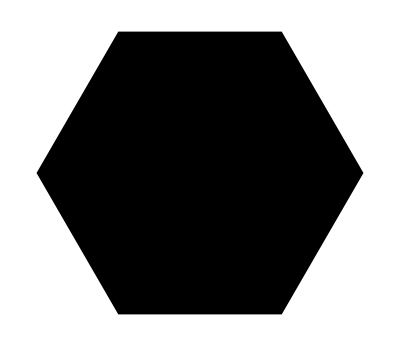

```mathematica
Show[WZC]
```

```mathematica
cell=Graphics[{{FaceForm[{Green,Opacity[0.2]}],EdgeForm[{Black,Dashed}],Polygon[#⟦;;2⟧&/@{{0,0,0},e1,e1+e2,e2}]},{Purple,Thick,Arrow[{{0,0},e1⟦;;2⟧}],Arrow[{{0,0},e2⟦;;2⟧}]}}];
```

```mathematica
cellAff=Graphics[{{FaceForm[{Green,Opacity[0.2]}],EdgeForm[{Black,Dashed}],Polygon[{{0,0},{0,1},{1,1},{1,0}}]},{Purple,Thick,Arrow[{{0,0},{0,1}}],Arrow[{{0,0},{1,0}}]}}];
```

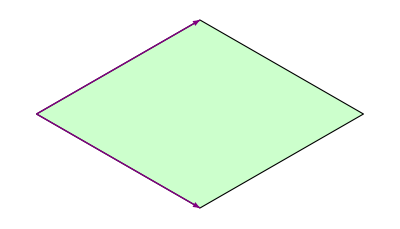

```mathematica
Show[cell]
```

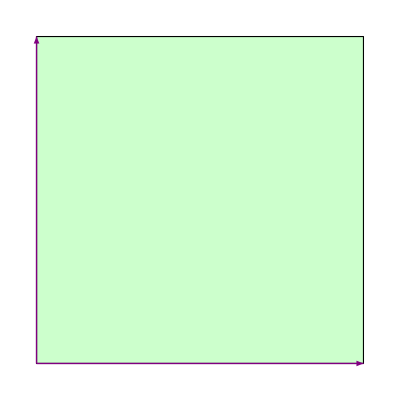

```mathematica
Show[cellAff]
```

### Ground state magnetization

```mathematica
μAll=Flatten[Join[Table[{Subscript[μ, 1][n1,n2],Subscript[μ, 2][n1,n2],Subscript[μ, 3][n1,n2]},{n1,-NN,NN},{n2,1,NN}],Table[{Subscript[μ, 1][n1,0],Subscript[μ, 2][n1,0],Subscript[μ, 3][n1,0]},{n1,0,NN}]]]; (* Declaration of the used Fourier components *)
```

```mathematica
M[n1_,n2_]:={ⅈ Subscript[μ, 1][n1,n2],ⅈ Subscript[μ, 2][n1,n2],Subscript[μ, 3][n1,n2]}; (* Covariant components of Fourier transform of m *)
```

```mathematica
rpl=Join[Table[{Subscript[μ, 1][n1,n2]->-Subscript[μ, 1][-n1,-n2],Subscript[μ, 2][n1,n2]->-Subscript[μ, 2][-n1,-n2],Subscript[μ, 3][n1,n2]->Subscript[μ, 3][-n1,-n2]},{n1,-NN,NN},{n2,-NN,-1}],Table[{Subscript[μ, 1][n1,0]->-Subscript[μ, 1][-n1,0],Subscript[μ, 2][n1,0]->-Subscript[μ, 2][-n1,0],Subscript[μ, 3][n1,0]->Subscript[μ, 3][-n1,0]},{n1,-NN,-1}]]//Flatten; (* Taking into account the symmetries of the Fourier components of magnetization*)
```

```mathematica
hexagon = Join[Table[{Subscript[μ, 1][n1,n2]->0,Subscript[μ, 2][n1,n2]->0,Subscript[μ, 3][n1,n2]->0},{n1,-NN,-1},{n2,1+n1+NN,NN}], {{Subscript[μ, 1][0,0]->0,Subscript[μ, 2][0,0]->0}}]//Flatten; (* Together with rpl reduction we already take into account all the relevant components *)
```

```mathematica
mGrHexagon[ξ1_,ξ2_(* Coordinates ξ^1 and ξ^2 in affine frame of reference *),
μFour_(*Fourier components of the magnetization*)]:=Sum[M[n1,n2] ⅇ^(ⅈ G[n1,n2].{ξ1,ξ2,0}),{n1,-NN,NN},{n2,-NN,NN}]/.rpl/.hexagon/.μFour;
```

```mathematica
A0=a0/.μVec (* Lattice constant *)
```

7.491740475541095127695131263986588674084

```mathematica
M0[n1_,n2_]:=If[Abs[n1]≤NN&&Abs[n2]≤NN,M[n1,n2]/.rpl/.hexagon/.μVec,{0,0,0}];(* Covariant components of Fourier transform of m *)
```

```mathematica
M0c[μ1_, μ2_] = toCRT[M0[μ1, μ2]]; (* Cartesian components of Fourier transform of m *)
```

```mathematica
M0FourierSpace = ListPlot3D[Table[M0[nn, mm][[3]],{nn,-NN,NN},{mm,-NN,NN}], Mesh->All, PlotRange->All, AxesLabel->{y, x, z}];
```

```mathematica
m0[x_, y_] = mGrHexagon[ξ1[x,y],ξ2[x,y],μVec];
```

```mathematica
m0C[η1_,η2_]=mGrHexagon[η1,η2,μVec].EE;(* Cartesian components of the magnetization vector, which depend on the affine coordinates η^1 and η^2.*)
```

```mathematica
range = 0.8;
```

```mathematica
den=DensityPlot[m0[x,y]⟦3⟧,{x,-range+x0,range+x0},{y,-range+y0,range+y0},PlotPoints->80,ColorFunction->"LightTemperatureMap", ColorFunctionScaling->True ,AspectRatio->1,FrameLabel->{"x/a_0","y/a_0"},LabelStyle->Large,PlotRange->All,PlotLegends->BarLegend[Automatic,LegendLabel->"m_z"],PlotRangePadding->None,ImageSize->500];
```

```mathematica
vct=VectorPlot[Re[toCRT[m0[x,y]]⟦;;2⟧],{x,-range+x0,range+x0},{y,-range+y0,range+y0},VectorScaling->Automatic,VectorAspectRatio->0.33,VectorColorFunction->None,VectorStyle->{RGBColor[0.2, 0.2, 0.2],Thick},VectorPoints->25,FrameStyle->Black,LabelStyle->Large,PlotRangePadding->None,FrameLabel->{"x/a_0","y/a_0"}, ImageSize->500(*,VectorMarkers->"Dart"*)];
```

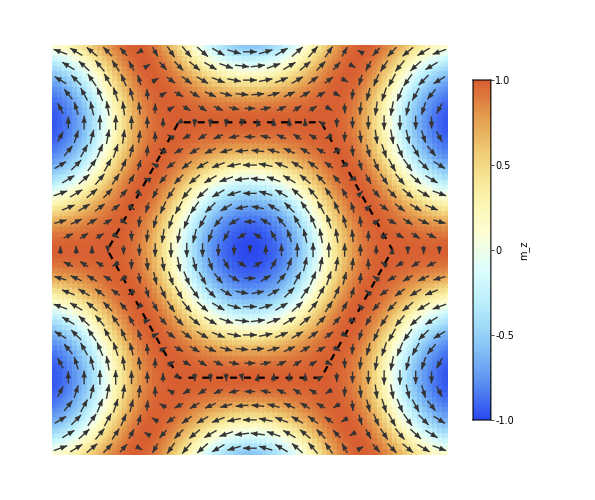

```mathematica
pPlot = Show[den,vct, RegionPlot[WZC, PlotStyle->None,BoundaryStyle->{Thick, Dashed, Black}]]
```

## Spectrum calculation

### Magnon dynamics

#### Matrix element of the functional derivative

```mathematica
v=Flatten[Join[Table[{n1,n2},{n1,-NN,0},{n2,-NN,NN + n1}], Table[{n1,n2},{n1,1,NN},{n2,-NN+n1,NN}]],1]; (* List of the used nodes of the reciprocal space reduced according to the hexagonal symmetry *)
```

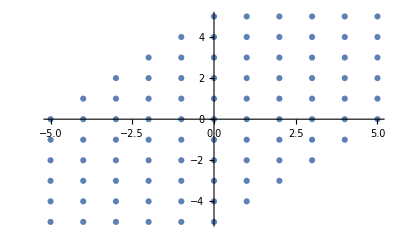

```mathematica
ListPlot[v]
```

```mathematica
(* Functions needed for the magnetostatic energy calculation *)
gms[η_]:=(η+ⅇ^-η-1)/η;gmsP[η_,σ_]:=(η+ⅇ^-η-1)/η+4/η Sinh[η/2]^2/(ⅇ^(η+σ)-1);
fms[η_]:=(1-ⅇ^-η)/η;fmsP[η_,σ_]:=(1-ⅇ^-η)/η-4/η Sinh[η/2]^2/(ⅇ^(η+σ)-1);
```

```mathematica
(* Geometrical parameters *)
n={0,0,1};(* Covariant components of the unit normal. Needed for the magnetostatics calculation *)
ed={0,0,1};(* Covariant components of the unit vector for Neel DMI. For the interfacial DMI ed==n *)
ea={0,0,1}; (* Unit vector along the anisotropy axis, covariant components. *)
(*L=1;h=0.5;*)
Nij = DiagonalMatrix[NijCRT];
```

```mathematica
S[α_(* Gilbert damping *)]:=IdentityMatrix[3Length[v]]-α Mx; (* Matrix S, introduced in (52) *)
```

```mathematica
J[k_List (* Wave vector, covariant components *),u_List (* Current vector, covariant components *)]:=ⅈ ArrayFlatten[ParallelTable[DotC[u,k+G[Sequence@@n]]IdentityMatrix[3]KroneckerDelta[n⟦1⟧,s⟦1⟧]KroneckerDelta[n⟦2⟧,s⟦2⟧],{n,v},{s,v}]];(* Matrix J, introduced in (52) *)
```

```mathematica
u={0,0,0}; (* Current vector, covariant components *)
α=0 ; (* 10^-4 Gilbert damping *)
λ=1; (*0.45*) (* Artificial damping responsible for the change of |m| *)
k = {0,0,0}; (* Wave vector covariant components *)
```

```mathematica
(* Calculation with the Hessian matrix *)
```

```mathematica
rijC[k_List (* Cartesian wavevector *)] := (-2 λ0 + 1/2 k.k)IdentityMatrix[3]-ⅈ TensorContract[LeviCivitaTensor[3]⊗k, {{3,4}}]+ξms If[k.k==0, Nij, (k⊗k)/(k.k)];
```

```mathematica
Hk[k_List (* Cartesian wavevector *)] := ArrayFlatten[ParallelTable[q=k(* Cartesian wavevector in the 1st BZ *)+1/A0 toCRT[G[Sequence@@Q1]];
 rijC[q]KroneckerDelta[Q1⟦1⟧,Q2⟦1⟧]KroneckerDelta[Q1⟦2⟧,Q2⟦2⟧],{Q1,v},{Q2,v}]];
```

```mathematica
He = ArrayFlatten[ParallelTable[2 λ0 Sum[DotC[M0[Sequence@@(-Q3)], M0[Sequence@@(Q1-Q2+Q3)]], {Q3, v}] IdentityMatrix[3] + 4 λ0 Sum[TensorProduct[toCRT[M0[Sequence@@(-Q3)]], toCRT[M0[Sequence@@(Q1-Q2+Q3)]]], {Q3, v}], {Q1,v},{Q2,v}]];
```

#### M0× projection

```mathematica
Mx = ArrayFlatten[ParallelTable[TensorContract[LeviCivitaTensor[3]⊗toCRT[M0[Sequence@@(n-s)]],{{2,4}}],{n,v},{s,v}]];
```

```mathematica
Export[NotebookDirectory[]<>"/SkL ground state thesis/projection.PDF", plot];
```

```mathematica
ClearAll[MkreuzProj];
MkreuzProj:=Module[{ProjectionOp, ES},
ES=Eigensystem[Mx];
ProjectionOp = Sum[
If[Abs[ES[[1]][[n]]]>0.97, Outer[Times,ES[[2]][[n]],Conjugate[ES[[2]][[n]]]],0],
{n,1,Length[ES[[1]]]}];
ProjectionOp.Mx.ProjectionOp
];
```

```mathematica
(* Calculate inverse of MkreuzProj *)
```

```mathematica
ES=Eigensystem[Mx];
```

```mathematica
(* Show that Subscript[m, 0]× = ∑_n Subscript[λ, n] Subscript[v, n] Subscript[v, n]^* *)
ttt = Mx-Sum[ES[[1, n]] Outer[Times,ES[[2]][[n]],Conjugate[ES[[2]][[n]]]], {n, 1, 273}];
Chop[ttt, 10^-8]//MatrixForm;
```

```mathematica
(* Show that (Subscript[m, 0]×)^P = ∑_n ' Subscript[λ, n] Subscript[v, n] Subscript[v, n]^* where the sum is restricted to the eigenvectors Subscript[v, n] s.t. |Subscript[λ, n]|>cutoff *)
testTemp = Sum[
If[Abs[ES[[1]][[n]]]>0.97, ES[[1]][[n]] Outer[Times,ES[[2]][[n]],Conjugate[ES[[2]][[n]]]],0],
{n,1,Length[ES[[1]]]}];
ttt2 = MkreuzProj-testTemp;
Chop[ttt2, 10^-8]//MatrixForm;
```

```mathematica
testTempInv = Sum[
If[Abs[ES[[1]][[n]]]>0.97, 1/(ES[[1]][[n]])Outer[Times,ES[[2]][[n]],Conjugate[ES[[2]][[n]]]],0],
{n,1,Length[ES[[1]]]}];
testIdentity = testTempInv.MkreuzProj;
Chop[testIdentity, 10^-8]//MatrixForm;
```

#### LL equation

```mathematica
k = {0,0,0};
```

```mathematica
h=2 ⅈ MkreuzProj.(Hk[k]+ He);
```

```mathematica
egs=Select[Transpose[Eigensystem[h]//Chop],0<Re[#⟦1⟧]≤6(*&&Abs[Im[ⅈ#⟦1⟧]]<λ/50*)&]; (* Solution of EVP (52) with filtering the "zero"  modes *)
```

```mathematica
egs⟦All,1⟧
```

{5.44522,5.13291,4.86648,4.50454,4.43021,4.42966,4.41249,4.13558,3.69833,3.60983,3.18182,2.79511,2.45636,2.44978,1.89619,1.40854,1.11228,0.643347,0.233428,0.000412837}

### Eigenfunction analysis

#### Orthogonality between magnon modes

```mathematica
k={0,0,0};
```

```mathematica
egs=SortBy[Select[Transpose[Eigensystem[2 MkreuzProj.(Hk[k]+ He)]//Chop],0<Re[ⅈ#⟦1⟧]≤6&],Re[ⅈ#⟦1⟧]&];
```

```mathematica
ⅈ egs⟦All,1⟧
```

{0.000412837+0. ⅈ,0.233428+0. ⅈ,0.643347+0. ⅈ,1.11228+0. ⅈ,1.40854+0. ⅈ,1.89619+0. ⅈ,2.44978+0. ⅈ,2.45636+0. ⅈ,2.79511+0. ⅈ,3.18182+0. ⅈ,3.60983+0. ⅈ,3.69833+0. ⅈ,4.13558+0. ⅈ,4.41249+0. ⅈ,4.42966+0. ⅈ,4.43021+0. ⅈ,4.50454+0. ⅈ,4.86648+0. ⅈ,5.13291+0. ⅈ,5.44522+0. ⅈ}

```mathematica
norm  = Table[Conjugate[egs⟦mode,2⟧].(-ⅈ testTempInv).egs⟦mode,2⟧//Chop, {mode, 1, Length[egs⟦All,1⟧]}];
```

```mathematica
orthogonalityTable = Table[1/(√(norm[[mode1]] norm[[mode2]]))Conjugate[egs⟦mode1,2⟧].(-ⅈ testTempInv).egs⟦mode2,2⟧//Chop, {mode1, 1, Length[egs⟦All,1⟧]}, {mode2, 1, Length[egs⟦All,1⟧]}];
```

```mathematica
Chop[orthogonalityTable, 10^-8]//MatrixForm
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

```mathematica
Nmode = 6;
ω0=ⅈ egs⟦Nmode,1⟧
Clear[temp];
temp = (1/(√norm[[Nmode]]))Partition[egs⟦Nmode,2⟧, 3];
efAffine[ξ1_,ξ2_]:=Sum[temp⟦Position[v, s][[1,1]]⟧ⅇ^(ⅈ G[s[[1]], s[[2]]].{ξ1,ξ2,0}), {s, v}];

efCRT[x_,y_]= Sum[temp⟦Position[v, s][[1,1]]⟧ⅇ^(ⅈ toCRT[G[s[[1]], s[[2]]]].{x,y,0}),{s, v}];
```